%%%V[r] and VLX[r] taken from Eqs. (21), (22) and Appendix B, Zerilli-ansatz for Z
%%%and setting n=2, alp=0 and bet=r. See also: Dif-Equation for gam(r).nb!

```mathematica
V[r_]:=1/(2 r^5)(-12 r^3-24 r^2 gam[r]+2 r^2 (8 r-16 m[r])+28 r^2 m[r]+84 r gam[r] m[r]-8 r m[r]^2-72 gam[r] m[r]^2+8 r^3 gam'[r]-32 r^2 m[r] gam'[r]+32 r m[r]^2 gam'[r]-4 r^3 m'[r]-12 r^2 gam[r] m'[r]+8 r^2 m[r] m'[r]+24 r gam[r] m[r] m'[r])
```

```mathematica
VLX[r_]:=-1/(2 r^4 gam[r])(-4 r^3-16 r^2 gam[r]+6 r^2 m[r]+74 r gam[r] m[r]+6 r m[r]^2-84 gam[r] m[r]^2+8 r^3 gam'[r]-40 r^2 m[r] gam'[r]+48 r m[r]^2 gam'[r]+2 r^3 m'[r]-18 r^2 gam[r] m'[r]-8 r^2 m[r] m'[r]+36 r gam[r] m[r] m'[r]+8 r^3 gam'[r] m'[r]-16 r^2 m[r] gam'[r] m'[r]+2 r^3 m'[r]^2-2 r^4 gam''[r]+8 r^3 m[r] gam''[r]-8 r^2 m[r]^2 gam''[r]+2 r^2 gam[r] (r-2 m[r]) m''[r]+r (-6 m[r]^2+2 r m[r] (-5+8 m'[r]-2 r m''[r])+r^2 (6+r m''[r]+2 m'[r] (-2-3 m'[r]+r m''[r]))))
```

%%%Definition of mass-function

```mathematica
m[r]:=1-27/(32 r^3);
m'[r]:=D[m[r],r];
m''[r]:=D[m'[r],r];
Derivative[3][m][r]:=D[m''[r],r];
Derivative[4][m][r]:=D[Derivative[3][m][r],r]
```

%%%ANSATZ for the gam-function, see main body of the text of the article)

```mathematica
FF[r]:= 1 + (2 m'[r] - r m''[r])/2
```

```mathematica
gam[r]:= - (r^2/(2 r + 3 m[r] - r  m'[r])) FF[r]
```

```mathematica
gam'[r]:=D[gam[r],r];
gam''[r]:=D[gam'[r],r]
```

%%%New for m of V[r] and VLX[r], using the ga-function ansatz

```mathematica
FullSimplify[V[r]]
FullSimplify[VLX[r]]
```

(3 (3-2 r)^2 (3+4 r (1+r)) (-1476225+32 r^3 (69984+28431 r+8 r^3 (-4779+4 r (-567+r (513+8 r (3+2 r (3+2 r (1+r)))))))))/(256 r^10 (81-16 r^3 (3+2 r))^2)

24057/(256 r^10)-162/r^7-375/(16 r^6)+84/r^4+284/(9 r^3)-746/(81 r^2)-128/(9 r)-(64 (5265+r (-1881+194 r)))/(81 (243+32 r^4))-(48 (1917+16 r (135+r (-354+13 r))))/((81-16 r^3 (3+2 r))^2)+(16 (-927+8 r (-162+r (93+32 r))))/(9 (-81+16 r^3 (3+2 r)))

%%%COPY RESULTS for V[r] and VLX[r]

```mathematica
V[r_]=(3 (3-2 r)^2 (3+4 r (1+r)) (-1476225+32 r^3 (69984+28431 r+8 r^3 (-4779+4 r (-567+r (513+8 r (3+2 r (3+2 r (1+r)))))))))/(256 r^10 (81-16 r^3 (3+2 r))^2)
```

(3 (3-2 r)^2 (3+4 r (1+r)) (-1476225+32 r^3 (69984+28431 r+8 r^3 (-4779+4 r (-567+r (513+8 r (3+2 r (3+2 r (1+r)))))))))/(256 r^10 (81-16 r^3 (3+2 r))^2)

```mathematica
VLX[r_]=24057/(256 r^10)-162/r^7-375/(16 r^6)+84/r^4+284/(9 r^3)-746/(81 r^2)-128/(9 r)-(64 (5265+r (-1881+194 r)))/(81 (243+32 r^4))-(48 (1917+16 r (135+r (-354+13 r))))/((81-16 r^3 (3+2 r))^2)+(16 (-927+8 r (-162+r (93+32 r))))/(9 (-81+16 r^3 (3+2 r)))
```

24057/(256 r^10)-162/r^7-375/(16 r^6)+84/r^4+284/(9 r^3)-746/(81 r^2)-128/(9 r)-(64 (5265+r (-1881+194 r)))/(81 (243+32 r^4))-(48 (1917+16 r (135+r (-354+13 r))))/((81-16 r^3 (3+2 r))^2)+(16 (-927+8 r (-162+r (93+32 r))))/(9 (-81+16 r^3 (3+2 r)))

%%%Plot V[r] and VLX[r] in different ranges

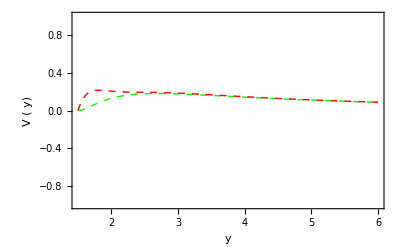

```mathematica
Plot[{V[y],VLX[y]},{y,1.5,6},Frame->True,PlotRange->{-1,1},FrameLabel->{Style[" y ",Large,Black],Style[" V ( y) ",Large,Black]}, PlotStyle->{{Green, Thick, Dashed},{Red, Thick,Dashed}}]
```

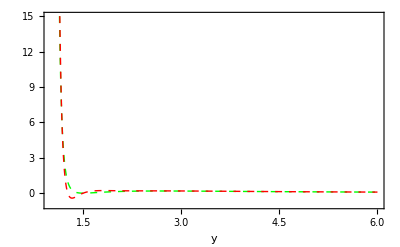

```mathematica
Plot[{V[y],VLX[y]},{y,1.,6},Frame->True,PlotRange->{-1,15},FrameLabel->{Style[" y ",Large,Black]}, PlotStyle->{{Green, Thick, Dashed},{Red, Thick,Dashed}}]
```